# Mетод на разполовяването

Задача: Да се реши уравнението (1. Да се намери броя на корените, 2. Да се уточни най-малкия корен по метода на разполовяването, 3. Да се направи оценка на грешката)
		x^3+45cos x + 6x -76 = 0
Да се изчисли предварително броят на стъпките (итерациите) за достигане на точност 0.00001 за определения по време на локализацията интервал по метода на разполовяването.

## Графично представяне на функцията

### Дефиниция на функция

```mathematica
f[x_]:=x^3+45Cos[x]+6x-76
```

### Графика на функция

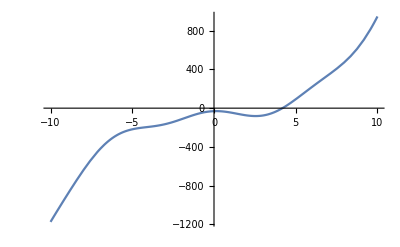

```mathematica
Plot[f[x],{x,-10,10}]
```

```mathematica
Plot[function,{var,min,max}]
```

Извод: Уравнението има един корен.

## Локализация на корен

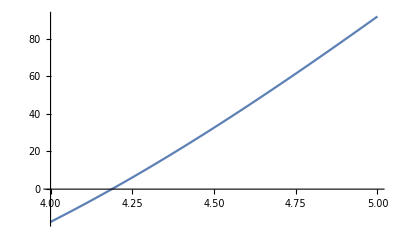

```mathematica
Plot[f[x],{x,4,5}]
```

```mathematica
f[4]
```

12+45 Cos[4]

```mathematica
f[4.]
```

-17.414

```mathematica
f[5.]
```

91.7648

Извод:
Функцията f(x) е непрекъсната, защото е сума от непрекъснати функции (полиним и косинус). 
f(4) = -17.4... < 0
f(5) = 91.76... > 0
Функцията има различни знаци в двата края на разглеждания интервал [4; 5]. 
Следователно  в този интервал [4; 5] функцията има корен.

## Уточняване на корен

### Уточнение за цикли и условни преходи

```mathematica
For[]
```

```mathematica
For[i=0,i<4,i++,Print[i]]
```

0

1

2

3

```mathematica
If[i<2, Print["малко"], Print["голямо"]]
```

голямо

```mathematica
i
```

4

```mathematica
For[i=0,i<4,i++,
(*body*)
Print[i];
If[i<2, Print["малко"], Print["голямо"]]
]
```

0

малко

1

малко

2

голямо

3

голямо

```mathematica
Clear[if]
if[i_]:= If[i<2, Print["малко"], Print["голямо"]]
For[i=0,i<4,i++,
(*body*)
Print[i];
if[i]
]
```

0

малко

1

малко

2

голямо

3

голямо

### програмен код за метода на разполовяването

```mathematica
f[x_]:=x^3+45Cos[x]+6x-76
a = 4.;
b = 5.;
For[n = 0, n<= 3, n++,
Print["n = ",n, " a = ",a, " b = ",b, " m = ",m = (a+b)/2, " f(m) = ",f[m], " ε = ",(b-a)/2];
If[f[m]<0,a=m,b=m]
]
```

n = 0 a = 4. b = 5. m = 4.5 f(m) = 32.6392 ε = 0.5

n = 1 a = 4. b = 4.5 m = 4.25 f(m) = 6.19169 ε = 0.25

n = 2 a = 4. b = 4.25 m = 4.125 f(m) = -5.99908 ε = 0.125

n = 3 a = 4.125 b = 4.25 m = 4.1875 f(m) = 0.00320478 ε = 0.0625

```mathematica
f[4.5]
```

32.6392

Извод: На третата стъпка получихме приближено решение 4.18... с грешка 0.06...

## Оценка на грешката

### Пускаме повече на брой итерации

```mathematica
f[x_]:=x^3+45Cos[x]+6x-76
a = 4.;
b = 5.;
For[n = 0, n<= 30, n++,
Print["n = ",n, " a = ",a, " b = ",b, " m = ",m = (a+b)/2, " f(m) = ",f[m], " ε = ",(b-a)/2];
If[f[m]<0,a=m,b=m]
]
```

n = 0 a = 4. b = 5. m = 4.5 f(m) = 32.6392 ε = 0.5

n = 1 a = 4. b = 4.5 m = 4.25 f(m) = 6.19169 ε = 0.25

n = 2 a = 4. b = 4.25 m = 4.125 f(m) = -5.99908 ε = 0.125

n = 3 a = 4.125 b = 4.25 m = 4.1875 f(m) = 0.00320478 ε = 0.0625

n = 4 a = 4.125 b = 4.1875 m = 4.15625 f(m) = -3.02171 ε = 0.03125

n = 5 a = 4.15625 b = 4.1875 m = 4.17188 f(m) = -1.51514 ε = 0.015625

n = 6 a = 4.17188 b = 4.1875 m = 4.17969 f(m) = -0.757428 ε = 0.0078125

n = 7 a = 4.17969 b = 4.1875 m = 4.18359 f(m) = -0.377476 ε = 0.00390625

n = 8 a = 4.18359 b = 4.1875 m = 4.18555 f(m) = -0.187227 ε = 0.00195313

n = 9 a = 4.18555 b = 4.1875 m = 4.18652 f(m) = -0.0920338 ε = 0.000976563

n = 10 a = 4.18652 b = 4.1875 m = 4.18701 f(m) = -0.0444202 ε = 0.000488281

n = 11 a = 4.18701 b = 4.1875 m = 4.18726 f(m) = -0.0206091 ε = 0.000244141

n = 12 a = 4.18726 b = 4.1875 m = 4.18738 f(m) = -0.00870252 ε = 0.00012207

n = 13 a = 4.18738 b = 4.1875 m = 4.18744 f(m) = -0.00274896 ε = 0.0000610352

n = 14 a = 4.18744 b = 4.1875 m = 4.18747 f(m) = 0.00022789 ε = 0.0000305176

n = 15 a = 4.18744 b = 4.18747 m = 4.18745 f(m) = -0.00126054 ε = 0.0000152588

n = 16 a = 4.18745 b = 4.18747 m = 4.18746 f(m) = -0.000516327 ε = 7.62939×10^-6

n = 17 a = 4.18746 b = 4.18747 m = 4.18747 f(m) = -0.000144219 ε = 3.8147×10^-6

n = 18 a = 4.18747 b = 4.18747 m = 4.18747 f(m) = 0.0000418353 ε = 1.90735×10^-6

n = 19 a = 4.18747 b = 4.18747 m = 4.18747 f(m) = -0.0000511918 ε = 9.53674×10^-7

n = 20 a = 4.18747 b = 4.18747 m = 4.18747 f(m) = -4.67821×10^-6 ε = 4.76837×10^-7

n = 21 a = 4.18747 b = 4.18747 m = 4.18747 f(m) = 0.0000185786 ε = 2.38419×10^-7

n = 22 a = 4.18747 b = 4.18747 m = 4.18747 f(m) = 6.95018×10^-6 ε = 1.19209×10^-7

n = 23 a = 4.18747 b = 4.18747 m = 4.18747 f(m) = 1.13598×10^-6 ε = 5.96046×10^-8

n = 24 a = 4.18747 b = 4.18747 m = 4.18747 f(m) = -1.77111×10^-6 ε = 2.98023×10^-8

n = 25 a = 4.18747 b = 4.18747 m = 4.18747 f(m) = -3.17564×10^-7 ε = 1.49012×10^-8

n = 26 a = 4.18747 b = 4.18747 m = 4.18747 f(m) = 4.0921×10^-7 ε = 7.45058×10^-9

n = 27 a = 4.18747 b = 4.18747 m = 4.18747 f(m) = 4.58226×10^-8 ε = 3.72529×10^-9

n = 28 a = 4.18747 b = 4.18747 m = 4.18747 f(m) = -1.35871×10^-7 ε = 1.86265×10^-9

n = 29 a = 4.18747 b = 4.18747 m = 4.18747 f(m) = -4.50241×10^-8 ε = 9.31323×10^-10

n = 30 a = 4.18747 b = 4.18747 m = 4.18747 f(m) = 3.9924×10^-10 ε = 4.65661×10^-10

печатаме с повече знака:

```mathematica
f[x_]:=x^3+45Cos[x]+6x-76
a = 4.;
b = 5.;
For[n = 0, n<= 30, n++,
Print["n = ",n, " a = ",SetPrecision[a,12], " b = ",SetPrecision[b,12], " m = ",SetPrecision[m = (a+b)/2,12], " f(m) = ",f[m], " ε = ",(b-a)/2];
If[f[m]<0,a=m,b=m]
]
```

n = 0 a = 4. b = 5. m = 4.5 f(m) = 32.6392 ε = 0.5

n = 1 a = 4. b = 4.5 m = 4.25 f(m) = 6.19169 ε = 0.25

n = 2 a = 4. b = 4.25 m = 4.125 f(m) = -5.99908 ε = 0.125

n = 3 a = 4.125 b = 4.25 m = 4.1875 f(m) = 0.00320478 ε = 0.0625

n = 4 a = 4.125 b = 4.1875 m = 4.15625 f(m) = -3.02171 ε = 0.03125

n = 5 a = 4.15625 b = 4.1875 m = 4.171875 f(m) = -1.51514 ε = 0.015625

n = 6 a = 4.171875 b = 4.1875 m = 4.1796875 f(m) = -0.757428 ε = 0.0078125

n = 7 a = 4.1796875 b = 4.1875 m = 4.18359375 f(m) = -0.377476 ε = 0.00390625

n = 8 a = 4.18359375 b = 4.1875 m = 4.185546875 f(m) = -0.187227 ε = 0.00195313

n = 9 a = 4.185546875 b = 4.1875 m = 4.1865234375 f(m) = -0.0920338 ε = 0.000976563

n = 10 a = 4.1865234375 b = 4.1875 m = 4.18701171875 f(m) = -0.0444202 ε = 0.000488281

n = 11 a = 4.18701171875 b = 4.1875 m = 4.18725585938 f(m) = -0.0206091 ε = 0.000244141

n = 12 a = 4.18725585938 b = 4.1875 m = 4.18737792969 f(m) = -0.00870252 ε = 0.00012207

n = 13 a = 4.18737792969 b = 4.1875 m = 4.18743896484 f(m) = -0.00274896 ε = 0.0000610352

n = 14 a = 4.18743896484 b = 4.1875 m = 4.18746948242 f(m) = 0.00022789 ε = 0.0000305176

n = 15 a = 4.18743896484 b = 4.18746948242 m = 4.18745422363 f(m) = -0.00126054 ε = 0.0000152588

n = 16 a = 4.18745422363 b = 4.18746948242 m = 4.18746185303 f(m) = -0.000516327 ε = 7.62939×10^-6

n = 17 a = 4.18746185303 b = 4.18746948242 m = 4.18746566772 f(m) = -0.000144219 ε = 3.8147×10^-6

n = 18 a = 4.18746566772 b = 4.18746948242 m = 4.18746757507 f(m) = 0.0000418353 ε = 1.90735×10^-6

n = 19 a = 4.18746566772 b = 4.18746757507 m = 4.1874666214 f(m) = -0.0000511918 ε = 9.53674×10^-7

n = 20 a = 4.1874666214 b = 4.18746757507 m = 4.18746709824 f(m) = -4.67821×10^-6 ε = 4.76837×10^-7

n = 21 a = 4.18746709824 b = 4.18746757507 m = 4.18746733665 f(m) = 0.0000185786 ε = 2.38419×10^-7

n = 22 a = 4.18746709824 b = 4.18746733665 m = 4.18746721745 f(m) = 6.95018×10^-6 ε = 1.19209×10^-7

n = 23 a = 4.18746709824 b = 4.18746721745 m = 4.18746715784 f(m) = 1.13598×10^-6 ε = 5.96046×10^-8

n = 24 a = 4.18746709824 b = 4.18746715784 m = 4.18746712804 f(m) = -1.77111×10^-6 ε = 2.98023×10^-8

n = 25 a = 4.18746712804 b = 4.18746715784 m = 4.18746714294 f(m) = -3.17564×10^-7 ε = 1.49012×10^-8

n = 26 a = 4.18746714294 b = 4.18746715784 m = 4.18746715039 f(m) = 4.0921×10^-7 ε = 7.45058×10^-9

n = 27 a = 4.18746714294 b = 4.18746715039 m = 4.18746714666 f(m) = 4.58226×10^-8 ε = 3.72529×10^-9

n = 28 a = 4.18746714294 b = 4.18746714666 m = 4.1874671448 f(m) = -1.35871×10^-7 ε = 1.86265×10^-9

n = 29 a = 4.1874671448 b = 4.18746714666 m = 4.18746714573 f(m) = -4.50241×10^-8 ε = 9.31323×10^-10

n = 30 a = 4.18746714573 b = 4.18746714666 m = 4.1874671462 f(m) = 3.9924×10^-10 ε = 4.65661×10^-10

Пресмятане с предварително зададена точност (стоп-критерий)

```mathematica
f[x_]:=x^3+45Cos[x]+6x-76
a = 4.;
b = 5.;
epszad = 0.00001;
eps = 10; (*произволна стойност по-голяма от предварително зададената грешка*)
For[n = 0, eps>epszad, n++,
Print["n = ",n, " a = ",SetPrecision[a,12], " b = ",SetPrecision[b,12], " m = ",SetPrecision[m = (a+b)/2,12], " f(m) = ",f[m], " ε = ",eps =(b-a)/2];
If[f[m]<0,a=m,b=m]
]
```

n = 0 a = 4. b = 5. m = 4.5 f(m) = 32.6392 ε = 0.5

n = 1 a = 4. b = 4.5 m = 4.25 f(m) = 6.19169 ε = 0.25

n = 2 a = 4. b = 4.25 m = 4.125 f(m) = -5.99908 ε = 0.125

n = 3 a = 4.125 b = 4.25 m = 4.1875 f(m) = 0.00320478 ε = 0.0625

n = 4 a = 4.125 b = 4.1875 m = 4.15625 f(m) = -3.02171 ε = 0.03125

n = 5 a = 4.15625 b = 4.1875 m = 4.171875 f(m) = -1.51514 ε = 0.015625

n = 6 a = 4.171875 b = 4.1875 m = 4.1796875 f(m) = -0.757428 ε = 0.0078125

n = 7 a = 4.1796875 b = 4.1875 m = 4.18359375 f(m) = -0.377476 ε = 0.00390625

n = 8 a = 4.18359375 b = 4.1875 m = 4.185546875 f(m) = -0.187227 ε = 0.00195313

n = 9 a = 4.185546875 b = 4.1875 m = 4.1865234375 f(m) = -0.0920338 ε = 0.000976563

n = 10 a = 4.1865234375 b = 4.1875 m = 4.18701171875 f(m) = -0.0444202 ε = 0.000488281

n = 11 a = 4.18701171875 b = 4.1875 m = 4.18725585938 f(m) = -0.0206091 ε = 0.000244141

n = 12 a = 4.18725585938 b = 4.1875 m = 4.18737792969 f(m) = -0.00870252 ε = 0.00012207

n = 13 a = 4.18737792969 b = 4.1875 m = 4.18743896484 f(m) = -0.00274896 ε = 0.0000610352

n = 14 a = 4.18743896484 b = 4.1875 m = 4.18746948242 f(m) = 0.00022789 ε = 0.0000305176

n = 15 a = 4.18743896484 b = 4.18746948242 m = 4.18745422363 f(m) = -0.00126054 ε = 0.0000152588

n = 16 a = 4.18745422363 b = 4.18746948242 m = 4.18746185303 f(m) = -0.000516327 ε = 7.62939×10^-6

Определяне на броя на итерациите за достигане на зададената точност:

```mathematica
Log2[(5-4)/0.00001]-1
```

15.6096